```mathematica
(* notebook to find energy density of stringbit *)
```

```mathematica
ClearAll[LoadEigenEnergies,LoadAndBucketEnergies,PlotEnergyBuckets];
DataFolder = NotebookDirectory[]<>"../data/";
Format[energy,StandardForm]="E";

Options[LoadEigenEnergies]={Folder->DataFolder,Bucketed->False, Single->False};
LoadEigenEnergies[s_,M_,opts:OptionsPattern[]]:=Module[{file,data},
file = "EEs="<> ToString[s] <> "M="<>ToString[M];
If[OptionValue[Single], file = file <>"s"];
If[OptionValue[Bucketed], file = file <>"g"];
data = Import[OptionValue[Folder]<> file <> ".txt", "Table"];
If[OptionValue[Bucketed]==False, data=Flatten[data]];
Return[data];
];

Options[LoadThermalData]={Folder->DataFolder};
LoadThermalData[s_,M_,opts:OptionsPattern[]]:=Module[{file,data},
file = "THs="<> ToString[s] <> "M="<>ToString[M];
data = Import[OptionValue[Folder]<> file <> ".txt", "Table"];
Return[data];
];

Options[LoadFluctuation]={Folder->DataFolder};
LoadFluctuation[s_,M_,opts:OptionsPattern[]]:=Module[{file,data},
file = "FLs="<> ToString[s] <> "M="<>ToString[M];
data = Import[OptionValue[Folder]<> file <> ".txt", "Table"];
Return[data];
];

PlotThermalData[s_,M_]:=Module[{data,Zdata,Edata,Sdata,ESdata,p1,p2,p3,p4},
data = LoadThermalData[s,M];
Zdata = Table[{data[[i, 1]],Log[data[[i,2]]]},{i,1,Length[data]}];
Edata = Table[{data[[i, 1]],data[[i,3]]},{i,1,Length[data]}];
Sdata = Table[{data[[i, 1]],data[[i,4]]},{i,1,Length[data]}];
ESdata = Table[{data[[i, 3]],data[[i,4]]},{i,1,Length[data]}];
p1=ListPlot[Zdata];
p2=ListPlot[Edata];
p3=ListPlot[Sdata];
p4=ListPlot[ESdata];
Return[{p1,p2,p3,p4}]
]

PlotFluctuation[s_,M_]:=Module[{data2,data,Z2},
data = LoadFluctuation[s,M];
Z2 = data[[1,2]]^2;
data2 = Table[{data[[i, 1]],(data[[i,2]]^2+data[[i,3]]^2)/Z2},{i,2,Length[data]}];
Return[ListPlot[data2]]
]


ClearAll[AverageEnergy];
Options[AverageEnergy]=Join[Options[LoadEigenEnergies],{}];
AverageEnergy[s_,M_, opts:OptionsPattern[]]:=Module[{data,data2,i,tot,count},
data = LoadEigenEnergies[s,M,FilterRules[{opts},Options[LoadEigenEnergies]]];
If[OptionValue[Bucketed]==False,
Return[Mean[data]],
tot=0;count=0;
For[i=1,i≤Length[data],i++,
tot += data[[i,1]] * data[[i,2]];
count += data[[i,2]]
];
Return[tot/count]
];
];

ClearAll[EnergyVariance];
Options[EnergyVariance]=Join[Options[LoadEigenEnergies],{}];
EnergyVariance[s_,M_, opts:OptionsPattern[]]:=Module[{data,data2},
data = LoadEigenEnergies[s,M,FilterRules[{opts},Options[LoadEigenEnergies]]];
data2=Table[data[[i]]^2,{i,1,Length[data]}];
Return[Mean[data2]-Mean[data]^2];
];

LoadAndBucketEnergies[s_,M_,n_]:=Module[{data,maxE,delta, buckets,i,pos},
data=LoadEigenEnergies[s,M];
maxE=N[4*s*Cot[Pi/(2M)]];
delta=2*maxE/n;
buckets=ConstantArray[0,n];
pos=Floor[(data+maxE)/delta] + 1;
For[i=1,i≤Length[pos],i++,
buckets[[pos[[i]]]]=buckets[[pos[[i]]]]+1;
];

Return[{Table[Chop[-maxE+delta*(i-0.5)],{i,1,n}],buckets}]
];

PlotEnergyBuckets[s_,M_,n_]:=Module[{data,i,list},
data=LoadAndBucketEnergies[s,M,n];
list=Table[{data[[1,i]],data[[2,i]]},{i,1,Length[data[[1]]]}];
(*Print[list];*)
ListPlot[list]
];

ClearAll[PlotEnergyBuckets];
Options[PlotEnergyBuckets]=Join[Options[LoadEigenEnergies],{}];
PlotEnergyBuckets[s_,M_,opts:OptionsPattern[]]:=Module[{data,tot,ndata,fit,p1,p2,p3,delta,i},
data=LoadEigenEnergies[s,M,FilterRules[{opts},Options[LoadEigenEnergies]]];
tot=Sum[data[[i,2]],{i,1,Length[data]}];
delta=data[[2,1]]-data[[1,1]];
ndata=Table[{data[[i,1]],data[[i,2]]/(tot*delta)},{i,1,Length[data]}];
fit=GaussianFit[ndata];
p1=ListPlot[ndata,AxesLabel->{"E", "ρ(E)"}(*,PlotLegends->{"Numerical"},PlotLabels->{"M="<>ToString[M]}*)];
p2=Plot[fit[x],{x, -N[4*s*Cot[Pi/(2M)]],N[4*s*Cot[Pi/(2M)]]}(*,PlotLegends->{"Gaussian Fit"}*)];
Show[p1,p2]
];

GaussianFit[ndata_]:=Module[{lmf},
lmf=NonlinearModelFit[ndata[[5;;Length[ndata]-5]], 
1/Sqrt[2*Pi*sigma^2]Exp[-(x-mu)^2/(2*sigma^2)],
{mu, sigma}, {x}];
Return[lmf]
];

ClearAll[FitEnergyData];
Options[FitEnergyData]=Join[Options[LoadEigenEnergies],{}];
FitEnergyData[s_, M_,opts:OptionsPattern[]]:=Module[{data, lmf, tot,ndata,delta},
data=LoadEigenEnergies[s,M,FilterRules[{opts},Options[LoadEigenEnergies]]];
tot=Sum[data[[i,2]],{i,1,Length[data]}];
delta=data[[2,1]]-data[[1,1]];
ndata=Table[{data[[i,1]],data[[i,2]]/(tot*delta)},{i,1,Length[data]}];
lmf=GaussianFit[ndata];
Return[{mu,sigma}/.lmf["BestFitParameters"]];
];
```

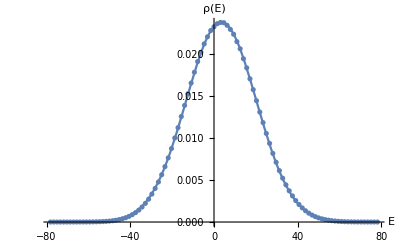
-Graphics-M=31

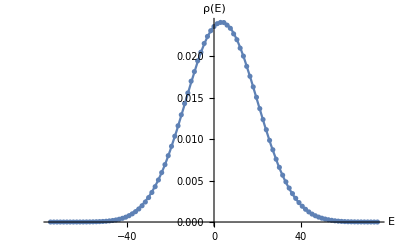

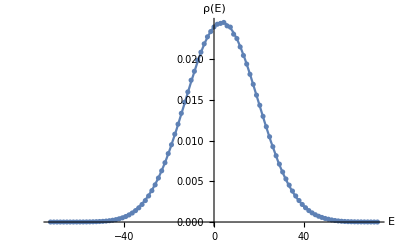

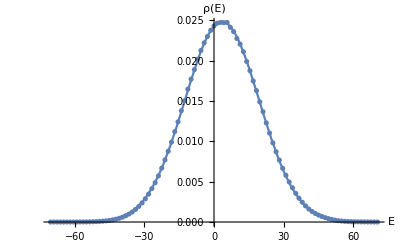

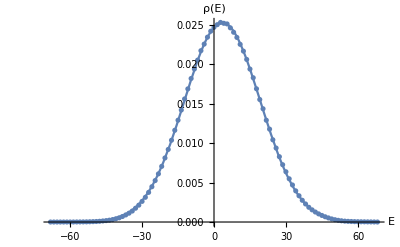

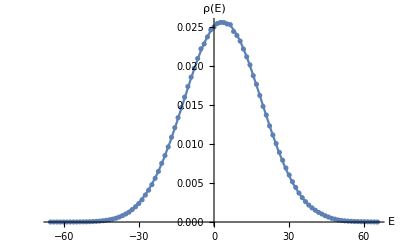

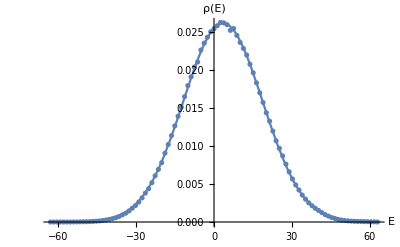

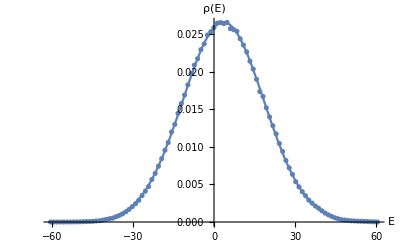

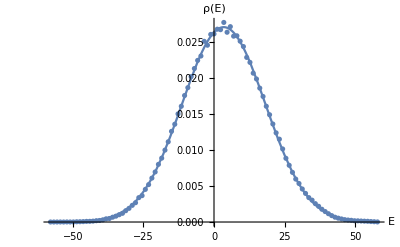

```mathematica
(*minM=19;
maxM=31;
For[ti=minM,ti≤maxM,ti++,
plot=Labeled[PlotEnergyBuckets[1,ti],"M="<>ToString[ti]];
Export["E-density-M"<>ToString[ti]<>".pdf",plot]
]
Clear[ti];*)
Labeled[PlotEnergyBuckets[1,31,Bucketed->True],"M=31"]
PlotEnergyBuckets[1,30,Bucketed->True]
PlotEnergyBuckets[1,29,Bucketed->True]
PlotEnergyBuckets[1,28,Bucketed->True]
PlotEnergyBuckets[1,27,Bucketed->True]
PlotEnergyBuckets[1,26,Bucketed->True]
PlotEnergyBuckets[1,25,Bucketed->True]
PlotEnergyBuckets[1,24,Bucketed->True]
PlotEnergyBuckets[1,23,Bucketed->True]
PlotEnergyBuckets[1,22,Bucketed->True]
PlotEnergyBuckets[1,21,Bucketed->True]
PlotEnergyBuckets[1,20,Bucketed->True]
```

{{19,3.40773,13.5941},{20,3.42988,13.9151},{21,3.43427,14.1918},{22,3.43657,14.4681},{23,3.43993,14.7429},{24,3.44837,15.0185},{25,3.45235,15.2834},{26,3.45492,15.5443},{27,3.459,15.8029},{28,3.46212,16.0556},{29,3.46318,16.304},{30,3.46702,16.5498},{31,3.46973,16.7917}}

{b→3.55675,c→2.6548}

{a→0.264925,b→8.62782}

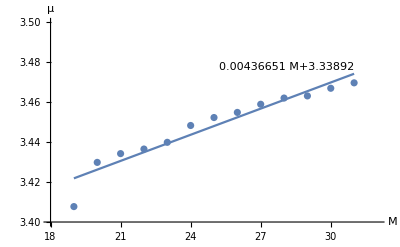

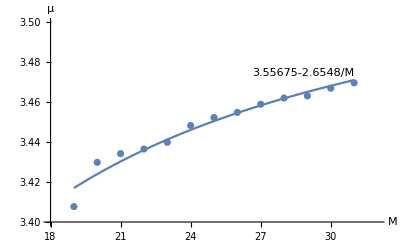

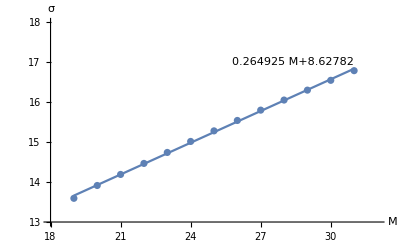

```mathematica
minM=19;
maxM = 31;
param=Table[Join[{m},FitEnergyData[1,m]],{m,minM,maxM}]
param1=param[[All,{1,2}]];
param2=param[[All,{1,3}]];
tfit1b=NonlinearModelFit[param1, a*M+b,{ b,a}, {M}];
tfit1=NonlinearModelFit[param1, b-c/M,{ b,c}, {M}];
tfit2=NonlinearModelFit[param2, a*M+b,{a, b}, {M}];

tplot1=Plot[tfit1[x],{x,minM,maxM},PlotLabels->Placed[Normal[tfit1],Above],AxesLabel->{"M", "μ"},PlotRange->{{18,32},{3.4,3.5}}];
tplot2=Plot[tfit2[x],{x,minM,maxM},PlotLabels->Placed[Normal[tfit2],Above],AxesLabel->{"M", "σ"},PlotRange->{{18,32},{13,18}}];
tfit1["BestFitParameters"]
tfit2["BestFitParameters"]

tplot1b=Plot[tfit1b[x],{x,minM,maxM},PlotLabels->Placed[Normal[tfit1b],Above],AxesLabel->{"M", "μ"},PlotRange->{{18,32},{3.4,3.5}}];
Show[tplot1b,ListPlot[param[[All,{1,2}]]]]
Export["mu.pdf",%];

Show[tplot1,ListPlot[param[[All,{1,2}]]]]
Export["fit-mu.pdf",%];
Show[tplot2,ListPlot[param[[All,{1,3}]]]]
Export["fit-sigma.pdf",%];
```

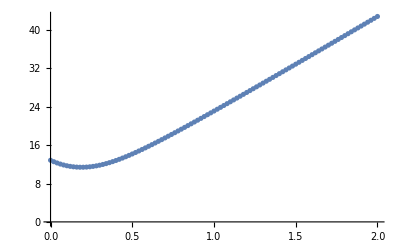

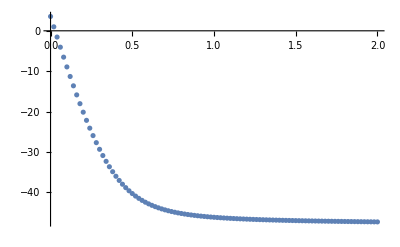

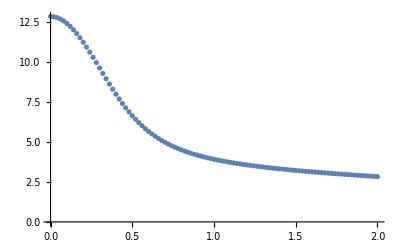

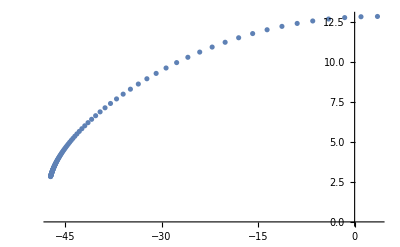

```mathematica
plots=PlotThermalData[1,19];
Show[plots[[1]]]
Show[plots[[2]]]
Show[plots[[3]]]
Show[plots[[4]]]
```

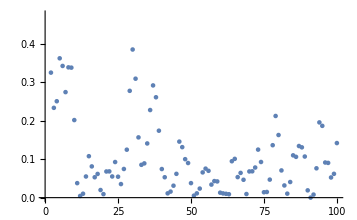

```mathematica
Show[PlotFluctuation[1,19]]
```

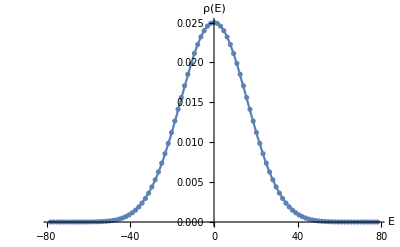

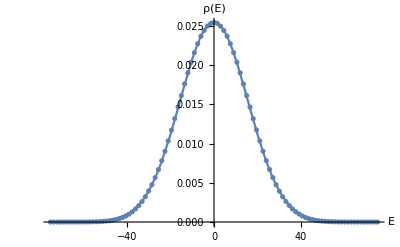

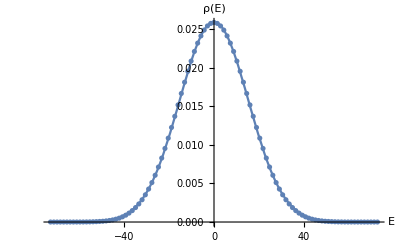

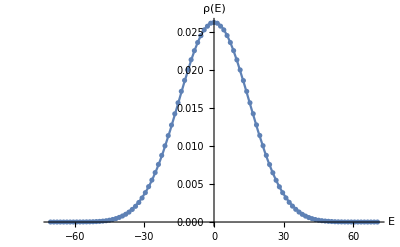

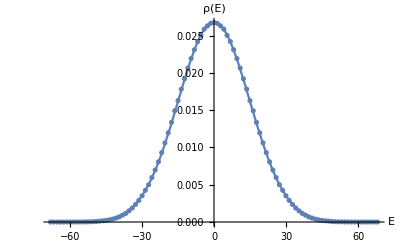

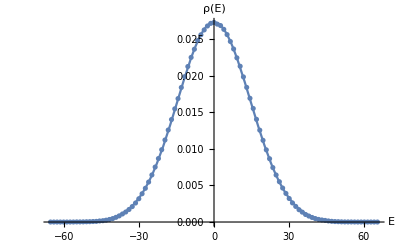

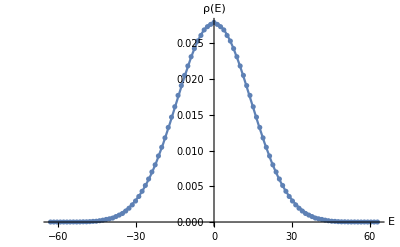

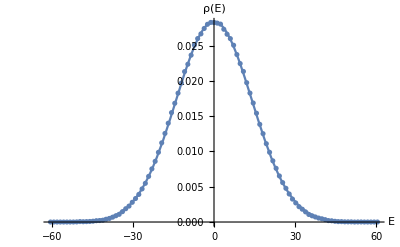

```mathematica
PlotEnergyBuckets[1,31,Bucketed->True,Single->True]
PlotEnergyBuckets[1,30,Bucketed->True,Single->True]
PlotEnergyBuckets[1,29,Bucketed->True,Single->True]
PlotEnergyBuckets[1,28,Bucketed->True,Single->True]
PlotEnergyBuckets[1,27,Bucketed->True,Single->True]
PlotEnergyBuckets[1,26,Bucketed->True,Single->True]
PlotEnergyBuckets[1,25,Bucketed->True,Single->True]
PlotEnergyBuckets[1,24,Bucketed->True,Single->True]
PlotEnergyBuckets[1,23,Bucketed->True,Single->True]
PlotEnergyBuckets[1,22,Bucketed->True,Single->True]
PlotEnergyBuckets[1,21,Bucketed->True,Single->True]
PlotEnergyBuckets[1,20,Bucketed->True,Single->True]
```

{b→-0.000245535,c→-0.00543784}

{a→0.280849,b→7.26729}

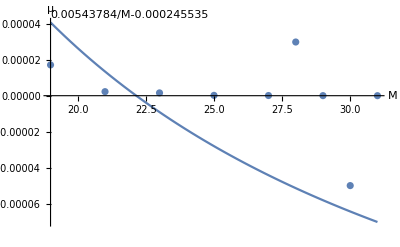

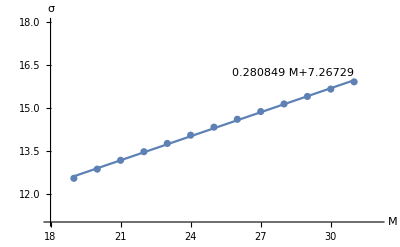

```mathematica
minM=19;
maxM = 31;
param=Table[Join[{m},FitEnergyData[1,m,Single->True,Bucketed->True]],{m,minM,maxM}];
param1=param[[All,{1,2}]];
param2=param[[All,{1,3}]];
tfit1=NonlinearModelFit[param1, b-c/M,{ b,c}, {M}];
tfit2=NonlinearModelFit[param2, a*M+b,{a, b}, {M}];

tfit1["BestFitParameters"]
tfit2["BestFitParameters"]

tplot1=Plot[tfit1[x],{x,minM,maxM},PlotLabels->Placed[Normal[tfit1],Above],AxesLabel->{"M", "μ"}];
tplot2=Plot[tfit2[x],{x,minM,maxM},PlotLabels->Placed[Normal[tfit2],Above],AxesLabel->{"M", "σ"},PlotRange->{{18,32},{11,18}}];
tplot1b=Plot[tfit1b[x],{x,minM,maxM},PlotLabels->Placed[Normal[tfit1b],Above],AxesLabel->{"M", "μ"}];

Show[tplot1,ListPlot[param[[All,{1,2}]]]]
(*Export["fit-mu.pdf",%];*)
Show[tplot2,ListPlot[param[[All,{1,3}]]]]
(*Export["fit-sigma-single.pdf",%];*)
```